```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
<<EcoEvo`
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

EcoEvo Package Version 1.7.3 (Nov 30, 2024)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
Clear[NTransformedDistribution];NTransformedDistribution[f_,ρin_:Automatic,{x_,xmin_?NumericQ,xmax_?NumericQ},opts___?OptionQ]:=Module[{ρ,breaks,sol,if,interpolationopts,ndsolveopts,ymax},

(* handle options *)
interpolationopts=Evaluate[InterpolationOpts/.Flatten[{opts,Options[NTransformedDistribution]}]];
ndsolveopts=Evaluate[NDSolveOpts/.Flatten[{opts,Options[NTransformedDistribution]}]];
ymax=Evaluate[MaxValue/.Flatten[{opts,Options[NTransformedDistribution]}]];

If[ρin===Automatic,ρ=1/(xmax-xmin),ρ=ρin];
(*Print[ρ];*)
breaks=DeleteDuplicates@Flatten[{N@xmin,FindExtrema[f,{x,xmin,xmax}][[All,1]],N@xmax}];
(*Print["breaks=",breaks];*)

(* not perfect but OK *)
Reinterpolation[
Sum[
sol=NDSolve[{
F[x]==f,
y[x]==Min[ymax,Abs[ρ/D[f,x]]],
z'[x]==0,z[xmin]==0
},{F,y},{x,breaks[[i]],breaks[[i+1]]},"ExtrapolationHandler"->{0&,"WarningMessage"->False},Evaluate[Sequence@@ndsolveopts]][[1]];

iff[i]=Interpolation[Union[
Transpose[{ExtractInterpolatingFunctionPoints[F/.sol][[All,2]],ExtractInterpolatingFunctionPoints[y/.sol][[All,2]]}],
SameTest->(Abs[#1[[1]]-#2[[1]]]<10^-8&)],
Evaluate[Sequence@@interpolationopts],"ExtrapolationHandler"->{0&,"WarningMessage"->False}]
,{i,1,Length[breaks]-1}],
Evaluate[Sequence@@interpolationopts],"ExtrapolationHandler"->{0&,"WarningMessage"->False}]
];

(* wrapping if *)
(*Reinterpolation[
Sum[
sol=NDSolve[{
F[x]==f,
y[x]==Min[ymax,Abs[ρ/D[f,x]]],
z'[x]==0,z[xmin]==0
},{F,y},{x,breaks[[i]],breaks[[i+1]]},Evaluate[Sequence@@ndsolveopts]][[1]];
Print[i," ",{breaks[[i]],breaks[[i+1]]}];
yMin=Min[breaks[[i]],breaks[[i+1]]];
yMax=Max[breaks[[i]],breaks[[i+1]]];
Print[i," ",{yMin,yMax}];
iff[i][yy_]:=0;
iff[i][yy_/;yMin<yy<yMax]=Interpolation[Union[
Transpose[{ExtractInterpolatingFunctionPoints[F/.sol][[All,2]],ExtractInterpolatingFunctionPoints[y/.sol][[All,2]]}],
SameTest->(Abs[#1[[1]]-#2[[1]]]<10^-8&)],
Evaluate[Sequence@@interpolationopts]][yy]
,{i,1,Length[breaks]-1}],
Evaluate[Sequence@@interpolationopts],"ExtrapolationHandler"->{0&,"WarningMessage"->False}]
];*)

Options[NTransformedDistribution]={NDSolveOpts->{},InterpolationOpts->{},MaxValue->100};
```

InterpolatingFunction[…]

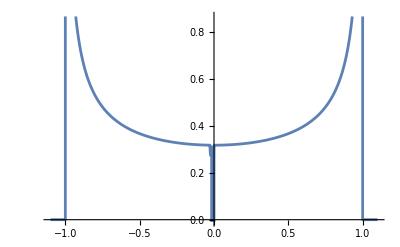

```mathematica
Clear[iff]
if=NTransformedDistribution[Sin[x],{x,0,2π}]
Plot[if[y],{y,-1.1,1.1}]
```

```mathematica
Table[iff[i]["Domain"],{i,3}]
```

{{{0.,1.}},{{-1.,1.}},{{-1.,-2.12604×10^-12}}}

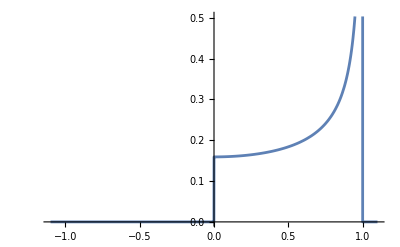
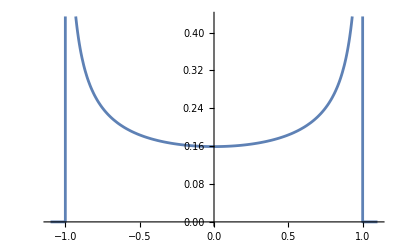
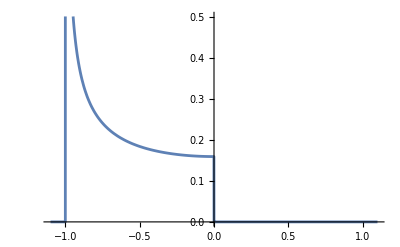

```mathematica
Table[Plot[iff[i][y],{y,-1.1,1.1}],{i,3}]
```

```mathematica
Table[iff[i][0],{i,3}]
```

{0.159155,0.159155,0.159155}

```mathematica
{Sum[iff[i][-0.001],{i,3}],Sum[iff[i][0],{i,3}],Sum[iff[i][0.001],{i,3}]}
```

{0.31831,0.477465,0.31831}

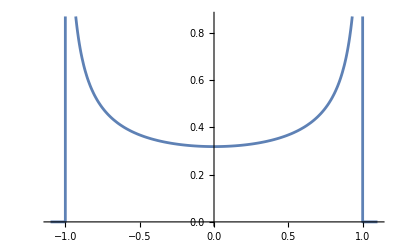

```mathematica
Plot[Sum[iff[i][y],{i,3}],{y,-1.1,1.1}]
```

```mathematica
reif=Reinterpolation[Sum[iff[i],{i,3}]]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {-1.09996} lies outside the range of data in the interpolating function. Extrapolation will be used.

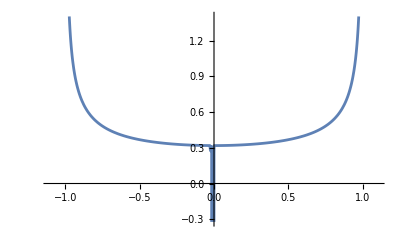

```mathematica
Plot[reif[y],{y,-1.1,1.1}]
```

```mathematica
pts
```

{{-1.,200.},{-1.,200.},{-1.,200.},{-1.,200.},{-1.,200.},{-0.999999,200.},{-0.999999,200.},{-0.999999,200.},{-0.999999,200.},{-0.999999,200.},{-0.999999,200.},{-0.999999,200.},{-0.999999,200.},{-0.999999,198.372},{-0.999999,199.302},{-0.999999,199.885},{-0.999999,200.02},{-0.999999,200.054},{-0.999999,199.93},{-0.999999,199.089},{-0.999999,199.013},{-0.999999,197.741},{-0.999999,197.169},{-0.999999,196.46},{-0.999999,196.226},{-0.999999,195.217},{-0.999999,194.173},{-0.999999,193.14},{-0.999999,192.142},{-0.999999,192.118},{-0.999999,191.106},{-0.999999,190.105},{-0.999999,188.224},{-0.999999,188.134},{-0.999999,186.485},{-0.999999,184.864},{-0.999999,184.463},{-0.999998,183.271},{-0.999998,181.437},{-0.999998,180.85},{-0.999998,179.639},{-0.999998,177.876},{-0.999998,177.375},{-0.999998,176.147},{-0.999998,174.452},{-0.999998,173.667},{-0.999998,172.789},{-0.999998,170.112},{-0.999998,169.556},{-0.999998,166.699},{-0.999998,166.442},{-0.999998,163.44},{-0.999998,163.064},{-0.999998,160.545},{-0.999998,159.584},{-0.999998,157.751},{-0.999998,156.249},{-0.999998,155.052},{-0.999998,153.051},{-0.999998,152.444},{-0.999998,149.981},{-0.999998,149.922},{-0.999998,147.482},{-0.999998,146.712},{-0.999998,145.121},{-0.999998,143.582},{-0.999998,142.833},{-0.999997,140.617},{-0.999997,140.582},{-0.999997,138.469},{-0.999997,137.706},{-0.999997,136.385},{-0.999997,134.944},{-0.999997,134.363},{-0.999997,132.4},{-0.999997,132.292},{-0.999997,130.494},{-0.999997,129.741},{-0.999997,128.641},{-0.999997,127.288},{-0.999997,126.841},{-0.999997,125.09},{-0.999997,124.925},{-0.999997,123.387},{-0.999997,122.648},{-0.999997,121.73},{-0.999997,120.453},{-0.999996,120.117},{-0.999996,118.545},{-0.999996,118.104},{-0.999996,117.015},{-0.999996,115.845},{-0.999996,115.523},{-0.999996,114.069},{-0.999996,113.671},{-0.999996,112.651},{-0.999996,111.577},{-0.999996,111.268},{-0.999996,109.919},{-0.999996,109.559},{-0.999996,108.602},{-0.999996,107.613},{-0.999996,107.316},{-0.999995,106.06},{-0.999995,105.734},{-0.999995,104.833},{-0.999995,103.722},{-0.999995,103.634},{-0.999995,102.462},{-0.999995,101.785},{-0.999995,101.317},{-0.999995,100.197},{-0.999995,99.7167},{-0.999995,99.1012},{-0.999995,98.0293},{-0.999995,97.7303},{-0.999995,96.9803},{-0.999994,95.9535},{-0.999994,95.8216},{-0.999994,94.9482},{-0.999994,93.9638},{-0.999994,93.7863},{-0.999994,92.9996},{-0.999994,92.055},{-0.999994,91.8357},{-0.999994,91.1293},{-0.999994,90.2221},{-0.999994,89.9646},{-0.999994,88.4609},{-0.999993,87.973},{-0.999993,86.767},{-0.999993,86.0677},{-0.999993,85.1368},{-0.999993,84.2432},{-0.999993,83.5668},{-0.999993,82.4944},{-0.999992,82.0536},{-0.999992,80.8167},{-0.999992,80.5943},{-0.999992,79.206},{-0.999992,79.1859},{-0.999992,77.8259},{-0.999992,77.6581},{-0.999991,76.5118},{-0.999991,76.1697},{-0.999991,75.2414},{-0.999991,74.7372},{-0.999991,74.0125},{-0.999991,73.3576},{-0.99999,72.8231},{-0.99999,72.0247},{-0.99999,71.6713},{-0.99999,70.5993},{-0.99999,70.5554},{-0.99999,69.4736},{-0.999989,69.2293},{-0.999989,68.4246},{-0.999989,67.9115},{-0.999989,67.4068},{-0.999989,66.5049},{-0.999989,66.4188},{-0.999988,65.4593},{-0.999988,65.1553},{-0.999988,64.5272},{-0.999988,63.8594},{-0.999987,63.6212},{-0.999987,62.7404},{-0.999987,62.6141},{-0.999987,61.8836},{-0.999987,61.4164},{-0.999986,61.0498},{-0.999986,60.2383},{-0.999986,60.1383},{-0.999986,59.448},{-0.999985,58.9122},{-0.999985,58.6782},{-0.999985,57.9281},{-0.999985,57.7352},{-0.999985,57.1969},{-0.999984,56.6043},{-0.999984,56.484},{-0.999984,55.7886},{-0.999984,55.5168},{-0.999983,55.1101},{-0.999983,54.448},{-0.999983,54.3565},{-0.999982,53.8015},{-0.999982,53.2437},{-0.999982,53.1702},{-0.999982,52.5536},{-0.999981,52.1755},{-0.999981,51.9511},{-0.999981,51.3622},{-0.999981,51.0379},{-0.99998,50.7866},{-0.99998,50.2237},{-0.99998,49.9488},{-0.999979,49.6732},{-0.999979,49.1346},{-0.999979,48.9052},{-0.999979,48.6075},{-0.999978,48.0917},{-0.999978,47.9043},{-0.999978,47.5867},{-0.999977,47.0921},{-0.999977,46.9435},{-0.999977,46.6078},{-0.999976,46.1333},{-0.999976,45.9203},{-0.999976,45.6684},{-0.999975,45.2127},{-0.999975,44.9406},{-0.999974,44.3282},{-0.999974,44.0019},{-0.999973,43.4775},{-0.999973,43.1017},{-0.999972,42.659},{-0.999972,42.2375},{-0.999971,41.8707},{-0.99997,41.4073},{-0.99997,41.1109},{-0.999969,40.6091},{-0.999969,40.3783},{-0.999968,39.8411},{-0.999968,39.6713},{-0.999967,39.1016},{-0.999967,38.9887},{-0.999966,38.3753},{-0.999966,38.3291},{-0.999964,37.6915},{-0.999964,37.5993},{-0.999963,37.0748},{-0.999963,36.854},{-0.999962,36.4779},{-0.999961,36.1377},{-0.999961,35.8999},{-0.99996,35.3738},{-0.999959,35.34},{-0.999958,34.7973},{-0.999958,34.6415},{-0.999957,34.2709},{-0.999956,33.939},{-0.999956,33.7603},{-0.999954,33.2647},{-0.999954,33.2643},{-0.999953,32.7834},{-0.999952,32.616},{-0.999951,32.3158},{-0.99995,31.9246},{-0.99995,31.8614},{-0.999949,31.4196},{-0.999948,31.262},{-0.999947,30.9898},{-0.999946,30.6263},{-0.999946,30.5717},{-0.999944,30.1647},{-0.999944,30.0159},{-0.999943,29.7684},{-0.999942,29.4294},{-0.999941,29.3824},{-0.99994,29.0062},{-0.999939,28.804},{-0.999938,28.6396},{-0.999937,28.2821},{-0.999936,28.2047},{-0.999935,27.9335},{-0.999934,27.6298},{-0.999933,27.5933},{-0.999932,27.2613},{-0.999931,27.0179},{-0.99993,26.9372},{-0.999929,26.6208},{-0.999927,26.4325},{-0.999927,26.3116},{-0.999925,26.0096},{-0.999924,25.8719},{-0.999923,25.7144},{-0.999922,25.4259},{-0.999921,25.3346},{-0.99992,25.1437},{-0.999918,24.8678},{-0.999918,24.8192},{-0.999916,24.5978},{-0.999914,24.3337},{-0.999914,24.2706},{-0.999913,24.0751},{-0.999911,23.822},{-0.99991,23.7457},{-0.999909,23.5742},{-0.999907,23.3315},{-0.999906,23.243},{-0.999905,23.0937},{-0.999903,22.8607},{-0.999902,22.7612},{-0.999901,22.6323},{-0.999898,22.299},{-0.999897,22.1891},{-0.999894,21.8551},{-0.999893,21.7629},{-0.99989,21.4286},{-0.999889,21.3527},{-0.999885,21.0184},{-0.999885,20.9577},{-0.999881,20.6236},{-0.99988,20.5771},{-0.999876,20.2434},{-0.999876,20.2101},{-0.999872,19.8769},{-0.999871,19.8559},{-0.999867,19.5235},{-0.999867,19.5139},{-0.999862,19.1835},{-0.999862,19.1453},{-0.999858,18.8641},{-0.999856,18.7814},{-0.999853,18.5552},{-0.999851,18.4311},{-0.999848,18.2562},{-0.999845,18.057},{-0.999843,17.9667},{-0.999838,17.6977},{-0.999838,17.6862},{-0.999833,17.4144},{-0.999832,17.3524},{-0.999828,17.1508},{-0.999825,17.0203},{-0.999823,16.8951},{-0.999818,16.7007},{-0.999817,16.6469},{-0.999812,16.4058},{-0.999811,16.3929},{-0.999806,16.1717},{-0.999804,16.0963},{-0.999801,15.9441},{-0.999796,15.7691},{-0.999795,15.7229},{-0.999789,15.5077},{-0.999788,15.4549},{-0.999784,15.2983},{-0.999778,15.1202},{-0.999778,15.0945},{-0.999772,14.8961},{-0.999769,14.7997},{-0.999766,14.7028},{-0.999759,14.5145},{-0.999759,14.4926},{-0.999753,14.3309},{-0.999749,14.1979},{-0.999747,14.1519},{-0.999741,13.9773},{-0.999738,13.9149},{-0.999734,13.807},{-0.999728,13.643},{-0.999728,13.6408},{-0.999721,13.4786},{-0.999717,13.3816},{-0.999714,13.3201},{-0.999708,13.1654},{-0.999706,13.1299},{-0.999701,13.0142},{-0.999695,12.8876},{-0.999694,12.8664},{-0.999687,12.722},{-0.999684,12.654},{-0.99968,12.5807},{-0.999673,12.4426},{-0.999672,12.4288},{-0.999665,12.3075},{-0.999659,12.1878},{-0.999658,12.1752},{-0.999651,12.0458},{-0.999646,11.9559},{-0.999643,11.9191},{-0.999636,11.7951},{-0.999632,11.7327},{-0.999628,11.6736},{-0.99962,11.5546},{-0.999616,11.4943},{-0.999613,11.4379},{-0.999601,11.2654},{-0.999597,11.2116},{-0.999583,11.0215},{-0.999581,10.9941},{-0.999565,10.7879},{-0.999564,10.7849},{-0.999548,10.5835},{-0.999546,10.5641},{-0.999531,10.3894},{-0.999527,10.3493},{-0.999513,10.2024},{-0.999507,10.1431},{-0.999495,10.0219},{-0.999485,9.92347},{-0.999477,9.8478},{-0.999463,9.71312},{-0.999459,9.6796},{-0.999441,9.51706},{-0.99944,9.51151},{-0.999422,9.35988},{-0.999414,9.29709},{-0.999402,9.20782},{-0.999387,9.09214},{-0.999383,9.06062},{-0.999363,8.91805},{-0.99936,8.89603},{-0.999343,8.77991},{-0.999332,8.70821},{-0.999322,8.64598},{-0.999303,8.52816},{-0.999301,8.51608},{-0.99928,8.39003},{-0.999271,8.33665},{-0.999259,8.26765},{-0.999238,8.15356},{-0.999237,8.1488},{-0.999215,8.03332},{-0.999204,7.97834},{-0.999192,7.92107},{-0.99917,7.81192},{-0.999169,7.8105},{-0.999146,7.70573},{-0.999134,7.64958},{-0.999123,7.6024},{-0.999099,7.5018},{-0.999098,7.49516},{-0.999075,7.40383},{-0.999061,7.34686},{-0.999051,7.30839},{-0.999026,7.21539},{-0.999023,7.20432},{-0.999001,7.12472},{-0.998985,7.06721},{-0.998976,7.0363},{-0.998951,6.95006},{-0.998946,6.93522},{-0.998925,6.8659},{-0.998906,6.80809},{-0.998899,6.78376},{-0.998872,6.70357},{-0.998866,6.68553},{-0.998845,6.62525},{-0.99882,6.55443},{-0.998818,6.54874},{-0.998791,6.47398},{-0.998773,6.42839},{-0.998763,6.40091},{-0.998735,6.32947},{-0.998726,6.3071},{-0.998706,6.25962},{-0.998677,6.19129},{-0.998677,6.19031},{-0.998648,6.12443},{-0.998628,6.07778},{-0.998619,6.05901},{-0.998589,5.99497},{-0.998574,5.96155},{-0.998559,5.93227},{-0.998529,5.87088},{-0.998518,5.84969},{-0.998468,5.75182},{-0.998456,5.73023},{-0.998405,5.63751},{-0.998392,5.61555},{-0.998341,5.52766},{-0.99832,5.49341},{-0.998275,5.42201},{-0.998246,5.37648},{-0.998209,5.32034},{-0.99817,5.26443},{-0.998141,5.22241},{-0.998085,5.1453},{-0.998072,5.12803},{-0.998001,5.037},{-0.997997,5.03144},{-0.99793,4.94916},{-0.997907,4.92253},{-0.997857,4.86433},{-0.997805,4.80692},{-0.997782,4.78237},{-0.997707,4.70314},{-0.997701,4.69664},{-0.99763,4.62649},{-0.997594,4.59131},{-0.997552,4.5523},{-0.997485,4.49061},{-0.997473,4.48046},{-0.997393,4.41086},{-0.997373,4.39424},{-0.997311,4.34339},{-0.997259,4.30193},{-0.997228,4.27797},{-0.997144,4.21449},{-0.997142,4.21344},{-0.997058,4.15287},{-0.997023,4.12852},{-0.996971,4.09303},{-0.996902,4.04696},{-0.996883,4.03489},{-0.996794,3.97839},{-0.996778,3.96857},{-0.996704,3.92346},{-0.996652,3.89317},{-0.996612,3.87003},{-0.996521,3.81911},{-0.996519,3.81803},{-0.996424,3.76742},{-0.996387,3.74782},{-0.996329,3.71814},{-0.99625,3.67915},{-0.996232,3.67014},{-0.996134,3.62336},{-0.996111,3.61296},{-0.996034,3.57777},{-0.995954,3.54216},{-0.995934,3.53331},{-0.995832,3.48995},{-0.995794,3.4741},{-0.995729,3.44765},{-0.99563,3.40861},{-0.995624,3.40636},{-0.995519,3.36605},{-0.995445,3.33869},{-0.995412,3.32669},{-0.995304,3.28825},{-0.995256,3.2716},{-0.995194,3.25069},{-0.995084,3.21398},{-0.995063,3.20717},{-0.994972,3.17809},{-0.994866,3.14523},{-0.994858,3.143},{-0.994744,3.10868},{-0.994665,3.08565},{-0.994628,3.07511},{-0.994511,3.04225},{-0.994444,3.02392},{-0.994274,2.97862},{-0.994219,2.96463},{-0.994031,2.91761},{-0.993964,2.90143},{-0.993783,2.85906},{-0.993703,2.84088},{-0.99353,2.80283},{-0.993407,2.77652},{-0.993273,2.74878},{-0.993104,2.71503},{-0.99301,2.69679},{-0.992794,2.65623},{-0.992742,2.64675},{-0.992469,2.59854},{-0.992442,2.59382},{-0.992191,2.55206},{-0.992081,2.53431},{-0.991908,2.50724},{-0.991712,2.47748},{-0.99162,2.46397},{-0.991335,2.42317},{-0.991328,2.42218},{-0.99103,2.3818},{-0.990949,2.3712},{-0.990727,2.34276},{-0.990555,2.32144},{-0.990419,2.30498},{-0.990152,2.27374},{-0.990106,2.26842},{-0.989788,2.23301},{-0.989742,2.22798},{-0.989465,2.1987},{-0.989322,2.18404},{-0.989137,2.16543},{-0.988895,2.14182},{-0.988804,2.13317},{-0.988466,2.10187},{-0.988459,2.10122},{-0.988123,2.07148},{-0.988015,2.06215},{-0.987775,2.04197},{-0.987512,2.02043},{-0.987423,2.0133},{-0.987065,1.98543},{-0.986998,1.98038},{-0.986702,1.95833},{-0.986474,1.9419},{-0.986334,1.93198},{-0.985961,1.90633},{-0.98588,1.90089},{-0.985583,1.88136},{-0.985273,1.86161},{-0.9852,1.85705},{-0.984813,1.83337},{-0.984584,1.81984},{-0.98442,1.81029},{-0.984022,1.7878},{-0.98388,1.77994},{-0.983619,1.76586},{-0.983212,1.74447},{-0.983159,1.74177},{-0.982799,1.7236},{-0.982382,1.70323},{-0.982341,1.70127},{-0.981959,1.68334},{-0.981531,1.66392},{-0.981503,1.66264},{-0.981099,1.64495},{-0.980661,1.62642},{-0.980646,1.62576},{-0.980219,1.60831},{-0.979671,1.58669},{-0.979319,1.5733},{-0.978672,1.54949},{-0.9784,1.5398},{-0.97765,1.51403},{-0.977461,1.50774},{-0.976604,1.48019},{-0.976502,1.47701},{-0.975534,1.44787},{-0.975523,1.44754},{-0.974525,1.41925},{-0.974441,1.41696},{-0.973506,1.39207},{-0.973324,1.38737},{-0.972469,1.36594},{-0.972184,1.35903},{-0.971411,1.3408},{-0.970889,1.3289},{-0.970334,1.31659},{-0.969566,1.30012},{-0.969237,1.29327},{-0.968213,1.2726},{-0.968121,1.27078},{-0.966985,1.24909},{-0.966677,1.24339},{-0.96583,1.22815},{-0.965104,1.21554},{-0.964655,1.20793},{-0.963496,1.18896},{-0.96346,1.18838},{-0.962246,1.16948},{-0.961668,1.16079},{-0.961013,1.1512},{-0.959796,1.13399},{-0.95976,1.1335},{-0.958488,1.11636},{-0.957664,1.10568},{-0.957197,1.09975},{-0.955886,1.08365},{-0.955479,1.0788},{-0.954555,1.06803},{-0.95324,1.05326},{-0.953206,1.05288},{-0.951837,1.03818},{-0.95069,1.02633},{-0.950449,1.0239},{-0.949042,1.01003},{-0.948073,1.00081},{-0.947616,0.996546},{-0.94617,0.983439},{-0.945391,0.976596},{-0.944705,0.970692},{-0.943222,0.95829},{-0.942643,0.95359},{-0.941719,0.94622},{-0.940197,0.934469},{-0.93983,0.931705},{-0.938656,0.923025},{-0.937096,0.911876},{-0.936952,0.910864},{-0.935517,0.901011},{-0.93392,0.89042},{-0.933677,0.888846},{-0.932303,0.880092},{-0.930668,0.870018},{-0.930323,0.867939},{-0.92734,0.850598},{-0.926888,0.848064},{-0.923938,0.832092},{-0.923375,0.829148},{-0.920461,0.814439},{-0.919782,0.811126},{-0.91691,0.797581},{-0.915698,0.792076},{-0.913285,0.78147},{-0.911517,0.773981},{-0.909585,0.766057},{-0.907239,0.756772},{-0.905813,0.7513},{-0.902374,0.738616},{-0.901967,0.73716},{-0.898048,0.723599},{-0.897391,0.721404},{-0.894056,0.710585},{-0.89229,0.705065},{-0.889992,0.698085},{-0.887074,0.689537},{-0.885857,0.686073},{-0.881741,0.674766},{-0.881649,0.674521},{-0.877371,0.663403},{-0.876293,0.660698},{-0.873021,0.652699},{-0.869719,0.644943},{-0.868601,0.642385},{-0.86411,0.632443},{-0.862987,0.630035},{-0.85955,0.622853},{-0.855323,0.614386},{-0.85492,0.613599},{-0.850222,0.604663},{-0.847468,0.599626},{-0.845454,0.596032},{-0.840618,0.58769},{-0.839422,0.585687},{-0.835714,0.579625},{-0.831187,0.572508},{-0.830743,0.571824},{-0.825704,0.564275},{-0.822767,0.560031},{-0.820599,0.556968},{-0.815427,0.549891},{-0.814162,0.548207},{-0.810189,0.543035},{-0.805374,0.536989},{-0.804886,0.536391},{-0.799518,0.529949},{-0.796405,0.526338},{-0.794085,0.523703},{-0.788588,0.517643},{-0.78623,0.51512},{-0.783027,0.511763},{-0.777403,0.506055},{-0.775838,0.504507},{-0.771716,0.500513},{-0.765967,0.495131},{-0.765231,0.494457},{-0.754283,0.484822},{-0.753197,0.483904},{-0.742355,0.475085},{-0.740905,0.473951},{-0.730187,0.465878},{-0.72836,0.464554},{-0.717783,0.457166},{-0.715566,0.455675},{-0.705147,0.448917},{-0.699175,0.44522},{-0.692283,0.4411},{-0.682409,0.435462},{-0.679195,0.433689},{-0.665887,0.426659},{-0.66335,0.425372},{-0.652364,0.419986},{-0.64385,0.416009},{-0.63863,0.41365},{-0.62469,0.407633},{-0.623923,0.407314},{-0.610547,0.401916},{-0.601297,0.398372},{-0.596207,0.396484},{-0.581674,0.391322},{-0.578178,0.390128},{-0.566954,0.386416},{-0.554585,0.382525},{-0.552049,0.381753},{-0.536967,0.377322},{-0.530537,0.375515},{-0.52171,0.373111},{-0.506285,0.369112},{-0.506054,0.369054},{-0.490697,0.365315},{-0.481157,0.363104},{-0.474949,0.36171},{-0.459048,0.358291},{-0.455865,0.357632},{-0.442999,0.35505},{-0.4302,0.352607},{-0.426806,0.351979},{-0.410475,0.349073},{-0.404182,0.348002},{-0.394012,0.346326},{-0.377833,0.343794},{-0.377421,0.343732},{-0.360708,0.341286},{-0.351174,0.339962},{-0.343879,0.338983},{-0.326938,0.33682},{-0.324228,0.336487},{-0.309892,0.334791},{-0.297015,0.333353},{-0.292745,0.332894},{-0.275504,0.331124},{-0.26956,0.330545},{-0.241883,0.328051},{-0.240759,0.327957},{-0.214008,0.325859},{-0.205703,0.325266},{-0.185958,0.32396},{-0.170382,0.323033},{-0.157755,0.322346},{-0.134839,0.321244},{-0.129423,0.32101},{-0.100984,0.319945},{-0.0991229,0.319885},{-0.0724635,0.319149},{-0.0632782,0.318949},{-0.0438832,0.318617},{-0.0273516,0.318429},{-0.0152669,0.318347},{-2.12604×10^-12,0.477465},{0.,0.477465},{0.0001,0.31831},{0.0002,0.31831},{0.0004,0.31831},{0.0008,0.31831},{0.0016,0.31831},{0.00319999,0.318311},{0.00639996,0.318316},{0.0127997,0.318336},{0.0133619,0.318338},{0.0255972,0.318414},{0.0383906,0.318545},{0.0419798,0.318591},{0.0511776,0.318728},{0.0639563,0.318963},{0.0705632,0.319105},{0.0767245,0.319251},{0.0990889,0.319884},{0.102221,0.319986},{0.127533,0.320931},{0.127651,0.320935},{0.152997,0.322102},{0.155873,0.322249},{0.178242,0.32349},{0.184085,0.323844},{0.203371,0.325104},{0.212147,0.325724},{0.228367,0.326949},{0.240034,0.327896},{0.253213,0.329033},{0.267725,0.33037},{0.277893,0.331361},{0.295196,0.333156},{0.302391,0.333944},{0.322425,0.336268},{0.326691,0.336789},{0.34939,0.33972},{0.350776,0.339908},{0.374632,0.343312},{0.376069,0.343528},{0.398242,0.347015},{0.402439,0.34771},{0.421592,0.351031},{0.42848,0.352287},{0.444665,0.355377},{0.454169,0.357284},{0.467446,0.36007},{0.479486,0.362726},{0.489922,0.365132},{0.50441,0.368643},{0.512076,0.370584},{0.516719,0.37179},{0.528921,0.375069},{0.533895,0.376453},{0.541015,0.378484},{0.552998,0.382041},{0.555363,0.382764},{0.564868,0.385745},{0.576468,0.389551},{0.576622,0.389603},{0.588258,0.39362},{0.597195,0.396848},{0.599774,0.397803},{0.611166,0.402159},{0.617531,0.404693},{0.622433,0.406696},{0.633573,0.411422},{0.637462,0.413131},{0.644583,0.416345},{0.655461,0.421474},{0.656976,0.422211},{0.666204,0.426821},{0.676058,0.431988},{0.676811,0.432394},{0.68728,0.438206},{0.694698,0.442526},{0.697607,0.444269},{0.707792,0.450595},{0.711085,0.452719},{0.717831,0.457199},{0.727094,0.463645},{0.727723,0.464096},{0.737467,0.471302},{0.739613,0.472949},{0.747059,0.478836},{0.751881,0.482801},{0.756498,0.486715},{0.763895,0.493243},{0.765782,0.494961},{0.774909,0.503597},{0.775649,0.504321},{0.783878,0.512646},{0.786003,0.514879},{0.792685,0.522135},{0.796141,0.526035},{0.801331,0.532093},{0.80606,0.537836},{0.809812,0.542552},{0.815758,0.550334},{0.818127,0.553546},{0.825232,0.563585},{0.826274,0.565113},{0.834252,0.577294},{0.834479,0.577653},{0.84206,0.590135},{0.843497,0.592608},{0.845899,0.596819},{0.849694,0.603688},{0.851415,0.606891},{0.853447,0.610748},{0.857155,0.618007},{0.859143,0.622021},{0.86082,0.625473},{0.86444,0.633155},{0.866681,0.638071},{0.868016,0.641061},{0.871548,0.6492},{0.8733,0.653368},{0.875035,0.657583},{0.878477,0.66622},{0.879761,0.66954},{0.881874,0.675122},{0.885226,0.684301},{0.886064,0.68666},{0.888533,0.693768},{0.8916,0.702945},{0.891794,0.703538},{0.895009,0.713623},{0.897006,0.720129},{0.898179,0.72404},{0.901303,0.734804},{0.90176,0.736424},{0.90438,0.745931},{0.906407,0.753563},{0.907411,0.757441},{0.910396,0.76935},{0.910946,0.771614},{0.913334,0.781681},{0.91494,0.788696},{0.916225,0.794455},{0.918846,0.806631},{0.919069,0.807696},{0.921866,0.821428},{0.922664,0.825481},{0.924616,0.835678},{0.926024,0.843286},{0.927319,0.850476},{0.929313,0.861945},{0.929974,0.865853},{0.93253,0.881518},{0.932581,0.881843},{0.935141,0.89848},{0.935674,0.902072},{0.937653,0.915805},{0.938746,0.923681},{0.940116,0.933861},{0.941745,0.946426},{0.942532,0.952692},{0.944671,0.970397},{0.944899,0.97235},{0.947218,0.992887},{0.947523,0.995693},{0.949488,1.01436},{0.950028,1.01968},{0.95171,1.03685},{0.952472,1.04492},{0.953883,1.0604},{0.954857,1.07152},{0.954951,1.07261},{0.956007,1.08511},{0.956952,1.09669},{0.957051,1.09792},{0.958082,1.11105},{0.958999,1.12314},{0.959101,1.12452},{0.960108,1.13833},{0.960996,1.15096},{0.961103,1.1525},{0.962085,1.16704},{0.962945,1.18025},{0.963055,1.18197},{0.964012,1.1973},{0.964845,1.21113},{0.964958,1.21305},{0.965891,1.22923},{0.966512,1.2404},{0.966811,1.24587},{0.967719,1.26298},{0.96814,1.27116},{0.968615,1.28059},{0.969498,1.29871},{0.969728,1.30355},{0.970369,1.31736},{0.971228,1.33658},{0.971276,1.33769},{0.972074,1.35639},{0.972635,1.37003},{0.972907,1.3768},{0.973729,1.39786},{0.973962,1.40402},{0.974537,1.4196},{0.975255,1.43979},{0.975334,1.44204},{0.976117,1.46521},{0.976392,1.47362},{0.976888,1.48917},{0.977502,1.50912},{0.977647,1.51394},{0.978393,1.53957},{0.978586,1.54641},{0.979127,1.5661},{0.979539,1.58163},{0.979848,1.59359},{0.98047,1.61852},{0.980557,1.62207},{0.981253,1.65162},{0.98138,1.65721},{0.981936,1.68228},{0.982181,1.69368},{0.982607,1.71413},{0.982964,1.73183},{0.983265,1.74722},{0.983653,1.76768},{0.983911,1.78165},{0.984329,1.80508},{0.984544,1.81748},{0.984991,1.84413},{0.985164,1.85481},{0.985638,1.88492},{0.985772,1.89372},{0.986271,1.9276},{0.986367,1.93433},{0.98689,1.97227},{0.98695,1.97675},{0.987237,1.99867},{0.987435,2.01432},{0.98752,2.02109},{0.9878,2.04403},{0.987969,2.05822},{0.988077,2.0675},{0.988351,2.09152},{0.988491,2.1041},{0.988622,2.11612},{0.988889,2.1413},{0.988951,2.1472},{0.989154,2.1671},{0.989401,2.19212},{0.989415,2.19354},{0.989673,2.22063},{0.989843,2.23898},{0.989928,2.24841},{0.99018,2.27691},{0.990275,2.28792},{0.990428,2.30614},{0.990674,2.33614},{0.990697,2.33906},{0.990916,2.36693},{0.991111,2.39257},{0.991155,2.39856},{0.991391,2.43106},{0.991514,2.4486},{0.991624,2.46445},{0.991853,2.49878},{0.991909,2.50735},{0.99208,2.53409},{0.992256,2.5627},{0.992303,2.57042},{0.992523,2.60782},{0.992596,2.62058},{0.99274,2.64633},{0.992928,2.68115},{0.992953,2.686},{0.993164,2.72689},{0.99322,2.73812},{0.993371,2.76905},{0.993506,2.79759},{0.993575,2.81254},{0.993776,2.85743},{0.993786,2.85972},{0.993974,2.90379},{0.994033,2.91806},{0.994168,2.95169},{0.994274,2.97884},{0.99436,3.0012},{0.994488,3.03576},{0.994548,3.05241},{0.994697,3.09492},{0.994733,3.10541},{0.994902,3.15644},{0.994915,3.16029},{0.995083,3.21395},{0.995093,3.21716},{0.995261,3.2736},{0.995269,3.27613},{0.995436,3.33552},{0.995441,3.3373},{0.995608,3.39984},{0.99561,3.40082},{0.995776,3.4667},{0.995776,3.46681},{0.995939,3.53542},{0.995941,3.53625},{0.996098,3.60682},{0.996102,3.60867},{0.996254,3.68117},{0.99626,3.68412},{0.996408,3.75867},{0.996416,3.76282},{0.996483,3.79866},{0.996558,3.83951},{0.996567,3.84495},{0.996631,3.88125},{0.996704,3.92392},{0.996716,3.93077},{0.996776,3.96753},{0.996848,4.01213},{0.996861,4.02052},{0.996918,4.05775},{0.996988,4.10442},{0.996989,4.10489},{0.997057,4.15217},{0.997114,4.19288},{0.997125,4.20106},{0.997193,4.25112},{0.997237,4.28474},{0.997259,4.30238},{0.997325,4.3549},{0.997345,4.37093},{0.99739,4.40872},{0.997451,4.46067},{0.997454,4.4639},{0.997518,4.52047},{0.997544,4.54466},{0.99758,4.5785},{0.997636,4.63188},{0.997642,4.63805},{0.997703,4.69916},{0.997726,4.72252},{0.997763,4.76192},{0.997814,4.81678},{0.997823,4.82637},{0.997881,4.8926},{0.997901,4.9149},{0.997939,4.96068},{0.997985,5.0171},{0.997996,5.03068},{0.998052,5.10269},{0.998068,5.12366},{0.998108,5.17679},{0.998142,5.22351},{0.998162,5.25308},{0.998213,5.32734},{0.998216,5.33166},{0.998269,5.41263},{0.998284,5.43539},{0.998321,5.4961},{0.998353,5.54792},{0.998373,5.5822},{0.99842,5.66522},{0.998424,5.67103},{0.998473,5.76275},{0.998486,5.78759},{0.998522,5.85748},{0.998551,5.91537},{0.998571,5.95539},{0.998614,6.04893},{0.998618,6.05663},{0.998665,6.16137},{0.998676,6.18868},{0.99871,6.26981},{0.998737,6.33504},{0.998755,6.38214},{0.99879,6.47282},{0.9988,6.49857},{0.998842,6.61673},{0.998843,6.61933},{0.998886,6.74467},{0.998893,6.7672},{0.998928,6.87486},{0.998938,6.9086},{0.998969,7.01018},{0.998982,7.05604},{0.999009,7.15094},{0.999025,7.20993},{0.999048,7.29747},{0.999063,7.35428},{0.999068,7.37301},{0.999087,7.45014},{0.9991,7.50453},{0.999106,7.52889},{0.999125,7.60934},{0.999133,7.64512},{0.999143,7.69152},{0.999162,7.77549},{0.999165,7.79107},{0.99918,7.86133},{0.999195,7.93377},{0.999198,7.94908},{0.999216,8.03881},{0.999224,8.08179},{0.999233,8.13059},{0.999251,8.2245},{0.999253,8.23544},{0.999268,8.3206},{0.999281,8.39506},{0.999285,8.41898},{0.999302,8.51971},{0.999309,8.56098},{0.999318,8.62288},{0.999333,8.71603},{0.999335,8.72859},{0.999351,8.83692},{0.999357,8.87681},{0.999367,8.94797},{0.99938,9.04363},{0.999383,9.06185},{0.999398,9.17867},{0.999403,9.21684},{0.999414,9.29855},{0.999426,9.39682},{0.999429,9.4216},{0.999444,9.54795},{0.999448,9.58398},{0.999459,9.67773},{0.99947,9.77875},{0.999474,9.8111},{0.999488,9.9482},{0.999491,9.9816},{0.999502,10.0892},{0.999512,10.1931},{0.999516,10.2342},{0.99953,10.3835},{0.999533,10.4137},{0.999544,10.5372},{0.999553,10.644},{0.999557,10.6955},{0.99957,10.8586},{0.999572,10.8848},{0.999583,11.0268},{0.999591,11.1368},{0.999596,11.2003},{0.999608,11.3737},{0.999609,11.3794},{0.999621,11.5643},{0.999625,11.621},{0.999633,11.7552},{0.999641,11.8792},{0.999645,11.9526},{0.999655,12.1217},{0.999657,12.1568},{0.999669,12.368},{0.999669,12.3742},{0.99968,12.5867},{0.999683,12.6375},{0.999691,12.8133},{0.999695,12.8843},{0.999702,13.0482},{0.999707,13.1408},{0.999713,13.2918},{0.999717,13.3807},{0.999724,13.5448},{0.999727,13.6294},{0.999734,13.8075},{0.999737,13.8747},{0.999744,14.0807},{0.999746,14.129},{0.999754,14.3649},{0.999755,14.3928},{0.999759,14.5113},{0.999764,14.6608},{0.999764,14.6667},{0.999769,14.8133},{0.999773,14.9512},{0.999774,14.9691},{0.999779,15.1282},{0.999782,15.2469},{0.999783,15.2907},{0.999788,15.4568},{0.999791,15.5546},{0.999793,15.6265},{0.999797,15.7999},{0.999799,15.875},{0.999802,15.9773},{0.999806,16.1586},{0.999807,16.2088},{0.99981,16.3442},{0.999815,16.534},{0.999815,16.557},{0.999819,16.7283},{0.999822,16.8834},{0.999823,16.9273},{0.999827,17.131},{0.999829,17.2229},{0.999831,17.3397},{0.999836,17.5536},{0.999836,17.5764},{0.99984,17.7727},{0.999843,17.9447},{0.999844,17.9975},{0.999848,18.2279},{0.999849,18.3287},{0.999851,18.4644},{0.999855,18.6887},{0.999855,18.7071},{0.999859,18.9562},{0.999861,19.0631},{0.999863,19.2121},{0.999866,19.4529},{0.999866,19.475},{0.99987,19.7452},{0.999872,19.8589},{0.999874,20.0229},{0.999877,20.2822},{0.999877,20.3086},{0.999881,20.6026},{0.999882,20.7239},{0.999884,20.9052},{0.999887,21.1383},{0.999887,21.2169},{0.999891,21.5379},{0.999891,21.5695},{0.999894,21.8689},{0.999896,22.0188},{0.999897,22.2101},{0.999899,22.4394},{0.9999,22.5622},{0.999903,22.8764},{0.999904,22.9256},{0.999907,23.2845},{0.999907,23.301},{0.99991,23.6888},{0.99991,23.7074},{0.999913,24.0897},{0.999913,24.1316},{0.999916,24.5045},{0.999916,24.5712},{0.999919,24.9338},{0.999919,25.0272},{0.999921,25.3784},{0.999922,25.5004},{0.999924,25.8392},{0.999925,25.9918},{0.999927,26.3169},{0.999928,26.5026},{0.99993,26.8127},{0.999931,27.0338},{0.999932,27.3276},{0.999933,27.5868},{0.999935,27.8626},{0.999936,28.1629},{0.999937,28.4189},{0.999939,28.7055},{0.999939,28.7635},{0.99994,28.998},{0.999941,29.2964},{0.999941,29.3264},{0.999942,29.6011},{0.999943,29.9118},{0.999943,29.9122},{0.999945,30.2299},{0.999946,30.521},{0.999946,30.5544},{0.999947,30.8859},{0.999948,31.1556},{0.999948,31.2247},{0.999949,31.571},{0.99995,31.8171},{0.99995,31.9251},{0.999951,32.2873},{0.999952,32.437},{0.999952,32.6577},{0.999954,33.0368},{0.999954,33.0814},{0.999955,33.4247},{0.999956,33.7521},{0.999956,33.8219},{0.999957,34.2286},{0.999957,34.4504},{0.999958,34.6452},{0.999959,35.0721},{0.999959,35.1783},{0.99996,35.5097},{0.999961,35.9376},{0.999961,35.9583},{0.999962,36.4183},{0.999962,36.6496},{0.999963,36.8903},{0.999964,37.3747},{0.999964,37.3903},{0.999965,37.872},{0.999965,38.1616},{0.999966,38.3827},{0.999966,38.8835},{0.999967,38.9074},{0.999967,39.4466},{0.999968,39.6332},{0.999968,40.001},{0.999969,40.3331},{0.999969,40.5711},{0.99997,41.0582},{0.99997,41.1578},{0.999971,41.7617},{0.999971,41.7881},{0.999972,42.3835},{0.999972,42.5444},{0.999973,43.0242},{0.999973,43.3287},{0.999973,43.6845},{0.999974,44.1424},{0.999974,44.3654},{0.999975,44.9872},{0.999975,45.0679},{0.999976,45.793},{0.999976,45.865},{0.999977,46.5418},{0.999977,46.7777},{0.999977,47.3154},{0.999978,47.7275},{0.999978,48.1153},{0.999979,48.7167},{0.999979,48.9426},{0.99998,49.7478},{0.99998,49.7989},{0.99998,50.6857},{0.99998,50.7138},{0.999981,51.6047},{0.999981,51.718},{0.999982,52.5576},{0.999982,52.7628},{0.999982,53.5463},{0.999983,53.8507},{0.999983,54.573},{0.999983,54.9844},{0.999984,55.6398},{0.999984,56.0464},{0.999984,56.7491},{0.999984,57.1502},{0.999985,57.3206},{0.999985,57.9036},{0.999985,58.2983},{0.999985,58.4987},{0.999985,59.1061},{0.999986,59.4935},{0.999986,59.7262},{0.999986,60.3595},{0.999986,60.7387},{0.999986,61.0063},{0.999987,61.6672},{0.999987,62.0372},{0.999987,62.3426},{0.999987,63.0329},{0.999987,63.2543},{0.999988,63.7387},{0.999988,64.4604},{0.999988,64.52},{0.999988,65.1987},{0.999988,65.8374},{0.999988,65.9541},{0.999989,66.7272},{0.999989,67.07},{0.999989,67.5186},{0.999989,68.3291},{0.999989,68.3496},{0.999989,69.1592},{0.99999,69.6789},{0.99999,70.0098},{0.99999,70.8815},{0.99999,71.061},{0.99999,71.7752},{0.99999,72.499},{0.99999,72.6918},{0.999991,73.632},{0.999991,73.9965},{0.999991,74.5969},{0.999991,75.5571},{0.999991,75.5875},{0.999991,76.6047},{0.999991,77.019},{0.999992,77.6496},{0.999992,78.5386},{0.999992,78.7234},{0.999992,79.8274},{0.999992,79.9584},{0.999992,80.9627},{0.999992,81.4305},{0.999992,82.1308},{0.999993,82.9578},{0.999993,83.3332},{0.999993,84.3823},{0.999993,84.5712},{0.999993,85.8466},{0.999993,85.8565},{0.999993,87.161},{0.999993,87.3831},{0.999994,88.5164},{0.999994,88.965},{0.999994,89.9145},{0.999994,90.6052},{0.999994,91.3575},{0.999994,92.3071},{0.999994,92.8476},{0.999994,94.0741},{0.999994,94.3871},{0.999994,95.91},{0.999995,95.9785},{0.999995,97.6245},{0.999995,97.8191},{0.999995,99.3279},{0.999995,99.8057},{0.999995,101.092},{0.999995,101.875},{0.999995,102.92},{0.999995,104.031},{0.999995,104.815},{0.999995,106.052},{0.999996,106.781},{0.999996,108.152},{0.999996,108.822},{0.999996,110.338},{0.999996,110.943},{0.999996,112.382},{0.999996,113.148},{0.999996,114.284},{0.999996,114.502},{0.999996,115.443},{0.999996,116.481},{0.999996,116.625},{0.999996,117.832},{0.999996,118.529},{0.999996,119.065},{0.999997,120.323},{0.999997,120.65},{0.999997,121.608},{0.999997,122.849},{0.999997,122.921},{0.999997,124.263},{0.999997,125.129},{0.999997,125.634},{0.999997,127.036},{0.999997,127.496},{0.999997,128.469},{0.999997,129.936},{0.999997,129.954},{0.999997,131.436},{0.999997,132.248},{0.999997,132.971},{0.999997,134.542},{0.999997,134.625},{0.999997,136.151},{0.999997,137.089},{0.999997,137.799},{0.999997,139.487},{0.999997,139.645},{0.999997,141.217},{0.999997,142.298},{0.999998,142.991},{0.999998,144.81},{0.999998,145.054},{0.999998,146.675},{0.999998,147.918},{0.999998,148.59},{0.999998,150.555},{0.999998,150.898},{0.999998,152.572},{0.999998,154.},{0.999998,154.645},{0.999998,156.774},{0.999998,157.233},{0.999998,158.963},{0.999998,160.605},{0.999998,161.214},{0.999998,163.53},{0.999998,164.124},{0.999998,165.913},{0.999998,167.801},{0.999998,168.366},{0.999998,170.894},{0.999998,171.253},{0.999998,173.498},{0.999998,174.851},{0.999998,176.183},{0.999998,178.604},{0.999998,178.952},{0.999998,181.81},{0.999998,182.521},{0.999999,184.76},{0.999999,186.272},{0.999999,186.613},{0.999999,187.808},{0.999999,189.37},{0.999999,190.457},{0.999999,190.958},{0.999999,192.573},{0.999999,194.216},{0.999999,194.462},{0.999999,194.78},{0.999999,195.487},{0.999999,196.398},{0.999999,197.411},{0.999999,198.425},{0.999999,198.642},{0.999999,199.349},{0.999999,199.601},{0.999999,199.945},{0.999999,200.064},{0.999999,200.038},{0.999999,200.},{0.999999,200.},{0.999999,200.},{0.999999,200.},{0.999999,200.},{0.999999,200.},{0.999999,200.},{0.999999,200.},{0.999999,200.},{0.999999,200.},{0.999999,200.},{0.999999,200.},{0.999999,200.},{1.,200.},{1.,200.},{1.,200.},{1.,200.}}

InterpolatingFunction[…]

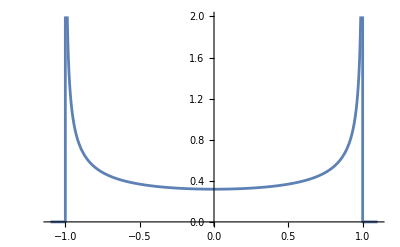

```mathematica
Clear[iff]
if=NTransformedDistribution[Sin[x],{x,0,2π-10^-5}]
Plot[if[y],{y,-1.1,1.1},PlotRange->{0,2}]
```

Interpolation::inddp: The point 0.841471 in dimension 1 is duplicated.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

InterpolatingFunction[…]

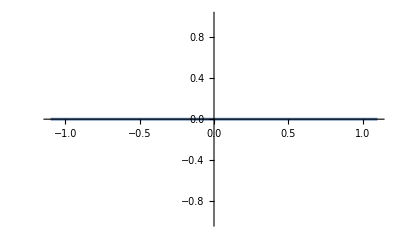

```mathematica
Clear[iff]
if=NTransformedDistribution[Sin[x],{x,1,2π+1}]
Plot[if[y],{y,-1.1,1.1}]
```